```mathematica
extractData[which_]:=Block[{r={},ns,xs={},ls},
ls=ReadList["~/PrismTech/Vortex-DDS PoC/Vortex-DDS PoC/"<>which<>"-res.txt",String];
Scan[Function[{l},
Block[{t},
t=StringCases[l,("NSUB "|"*********** ")~~x:NumberString->x];
If[Length[t]>0,
If[Length[xs]>0,AppendTo[r,{ns,Flatten[xs]}]];
ns=ToExpression[t[[1]]];xs={}];
t=StringCases[l,"Transfer rate: "~~x:NumberString->x];
If[Length[t]>0,xs={xs,ToExpression[t[[1]]]}];
]],ls];
If[Length[xs]>0,AppendTo[r,{ns,Flatten[xs]}]];
r];
```

```mathematica
rr=extractData["rr"];
rrmix=extractData["rrmix"];
rrmix1=extractData["rrmix-1"];
```

```mathematica
rrlitews=extractData["rrlite-ws"];
```

```mathematica
rrlite=extractData["rrlite"];
```

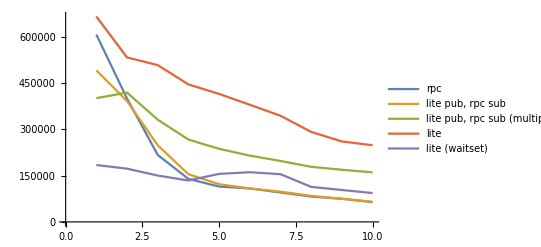

```mathematica
plot=ListPlot[{Median/@Last/@rr,Median/@Last/@rrmix,Median/@Last/@rrmix1,Median/@Last/@rrlite,Median/@Last/@rrlitews},Joined->True,PlotLegends->Placed[{"rpc","lite pub, rpc sub","lite pub, rpc sub (multiplexed)","lite","lite (waitset)"},Bottom]]
```

```mathematica
Export["~/PrismTech/PerfAnalysis/rpc-lite.png",plot]
```

~/PrismTech/PerfAnalysis/rpc-lite.png

```mathematica
rrmixb=extractData["rrmixb"];
rrmix1b=extractData["rrmix-1b"];
```

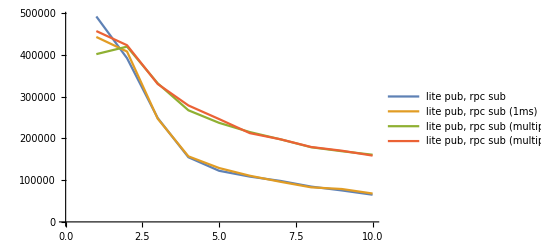

```mathematica
plot=ListPlot[{Median/@Last/@rrmix,Median/@Last/@rrmixb,Median/@Last/@rrmix1,Median/@Last/@rrmix1b},Joined->True,PlotLegends->Placed[{"lite pub, rpc sub","lite pub, rpc sub (1ms)","lite pub, rpc sub (multiplexed)","lite pub, rpc sub (multiplexed, 1ms"},Bottom]]
```

```mathematica
liteShortCircuit={9777950,8526195,7506163,6595059,6067183,5545528,5058146,4735008,4405061,3880621,3888308,3670521,3458788,3281181,3096084,2983591};
```

8.74838×10^-8+1.56256×10^-8 x

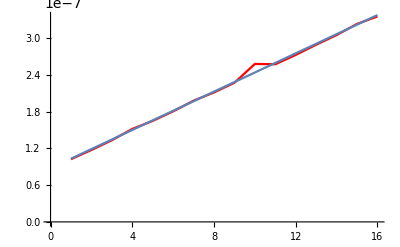

```mathematica
Fit[1/liteShortCircuit,{1,x},{x}]
Show[ListLinePlot[1/liteShortCircuit,PlotStyle->Red],Plot[%,{x,1,16}]]
```

```mathematica
osplShortCircuit={5.953877*^5,4.982163*^5,3.784905*^5,3.298967*^5,2.557979*^5,2.498771*^5,2.187898*^5,2.005900*^5,1.824454*^5,1.661058*^5,1.547313*^5,1.456155*^5,1.374050*^5,1.282814*^5,1.205297*^5,1.142767*^5};
```

1.22882×10^-6+4.71457×10^-7 x

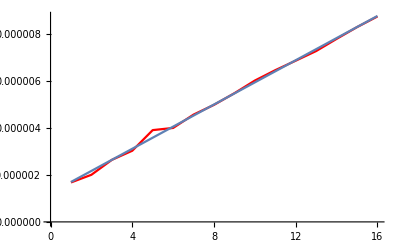

```mathematica
ospl=Fit[1/osplShortCircuit,{1,x},{x}]
Show[ListLinePlot[1/osplShortCircuit,PlotStyle->Red],Plot[ospl,{x,1,16}]]
```

```mathematica
osplShortCircuitSP={5.480513*^5,4.321109*^5,3.578454*^5,3.288934*^5,2.440005*^5,2.420241*^5,1.976315*^5,1.946464*^5,1.772107*^5,1.701394*^5,1.508496*^5,1.417972*^5,1.148222*^5,1.253000*^5,9.607818*^4,1.132796*^5};
```

1.16486×10^-6+5.21261×10^-7 x

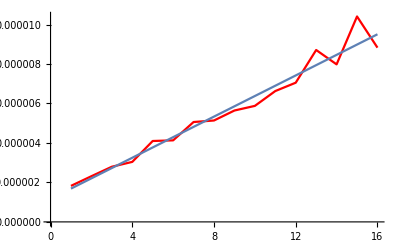

```mathematica
osplSP=Fit[1/osplShortCircuitSP,{1,x},{x}]
Show[ListLinePlot[1/osplShortCircuitSP,PlotStyle->Red],Plot[%,{x,1,16}]]
```

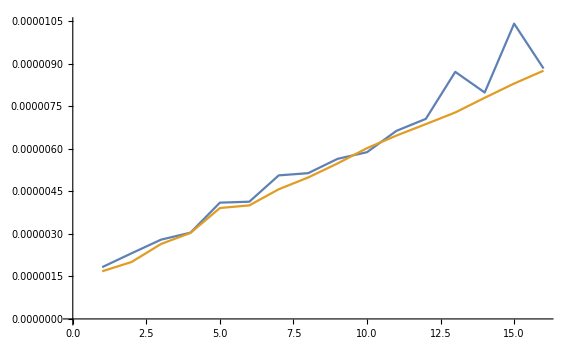

```mathematica
ListLinePlot[{1/osplShortCircuitSP,1/osplShortCircuit},ImageSize->Large]
```